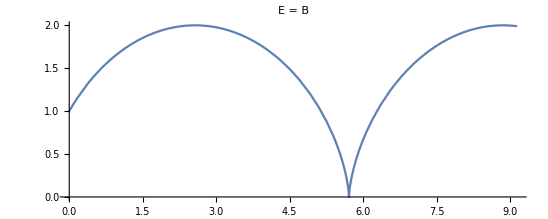

```mathematica
Clear["Global`*"]
Efield:= 1;
Bfield:= 1;
m:=1;
q:=1;
x[t_]:=x[t];
y[t_]:=y[t];
x[0]:=Subscript[x, 0];
y[0]:=Subscript[y, 0];
c:=1;
ω:= (q*Bfield)/(m*c)
A:=1+ⅈ*1;
Subscript[ξ, 0]:=1+ⅈ*1;
ξ[t_]:=ⅈ/(ω*c)*(A-(c*Efield)/Bfield)*ⅇ^(-ⅈ*ω*t)+(c*Efield)/Bfield*t+Subscript[ξ, 0];
ParametricPlot[{Re[ξ[t]],Im[ξ[t]]},{t,0,8},PlotLabel->"E = B"]
```

```mathematica
∑_(n=1)^∞ (2^(n-1)*1/4^n)
```

1/2

```mathematica
∑_(n=1)^∞ (2^(n-1)*1/3^n)
```

1

```mathematica
∑_(n=1)^∞ (2^(n-1)*3^(n-1)/4*1/8^(n-1))
```

1

```mathematica
∑_(n=1)^∞ (1/4*6^(n-1)/8^(n-1))
```

1

```mathematica
FullSimplify[Assuming[Element[σ,Reals]&&σ>0,∫_(5*σ)^∞ (1/(σ*Sqrt[2*π])*ⅇ^(-(x^2/(2*σ^2))))ⅆx]]
```

1/2 Erfc[5/(√2)]

```mathematica
N[%,10]
```

2.866515719×10^-7

```mathematica
∫_□^□ □ⅆ□
```

```mathematica
MomentOfInertia[Region[Disk[]]]//MatrixForm
```

(π/4 | 0
0 | π/4)

```mathematica
?MomentOfInertia
```

```mathematica
r[t_]:=l*{Cos[β]*(t-1/4),0,Sin[β]*(t-1/4)};
```

```mathematica
Inertia[i_,j_]:=∫_0^1 (m*((r[t].r[t])*KroneckerDelta[i,j]-r[t][[i]]*r[t][[j]]))ⅆt;
```

```mathematica
Inertia[3,1]
```

-7/48 l^2 m Cos[β] Sin[β]

```mathematica
Irod = Table[Table[Inertia[i,j],{i,1,3}],{j,1,3}]//MatrixForm
```

(7/48 l^2 m Sin[β]^2 | 0 | -7/48 l^2 m Cos[β] Sin[β]
0 | (7 l^2 m)/48 | 0
-7/48 l^2 m Cos[β] Sin[β] | 0 | 7/48 l^2 m Cos[β]^2)

```mathematica
Idisk=((m*R^2)/4*({{1, 0, 0}, {0, 1, 0}, {0, 0, 2}}) + (m*l^2)/16*({{Sin[β]^2, 0, -Cos[β] Sin[β]}, {0, 1, 0}, {-Cos[β] Sin[β], 0, Cos[β]^2}}))//MatrixForm
```

((m R^2)/4+1/16 l^2 m Sin[β]^2 | 0 | -1/16 l^2 m Cos[β] Sin[β]
0 | (l^2 m)/16+(m R^2)/4 | 0
-1/16 l^2 m Cos[β] Sin[β] | 0 | (m R^2)/2+1/16 l^2 m Cos[β]^2)

```mathematica
({{(m R^2)/4+1/16 l^2 m Sin[β]^2, 0, -1/16 l^2 m Cos[β] Sin[β]}, {0, (l^2 m)/16+(m R^2)/4, 0}, {-1/16 l^2 m Cos[β] Sin[β], 0, (m R^2)/2+1/16 l^2 m Cos[β]^2}})+({{7/48 l^2 m Sin[β]^2, 0, -7/48 l^2 m Cos[β] Sin[β]}, {0, (7 l^2 m)/48, 0}, {-7/48 l^2 m Cos[β] Sin[β], 0, 7/48 l^2 m Cos[β]^2}})//MatrixForm
```

((m R^2)/4+5/24 l^2 m Sin[β]^2 | 0 | -5/24 l^2 m Cos[β] Sin[β]
0 | (5 l^2 m)/24+(m R^2)/4 | 0
-5/24 l^2 m Cos[β] Sin[β] | 0 | (m R^2)/2+5/24 l^2 m Cos[β]^2)

```mathematica
Simplify[Eigenvectors[({{(m R^2)/4+5/24 l^2 m Sin[β]^2, 0, -5/24 l^2 m Cos[β] Sin[β]}, {0, (5 l^2 m)/24+(m R^2)/4, 0}, {-5/24 l^2 m Cos[β] Sin[β], 0, (m R^2)/2+5/24 l^2 m Cos[β]^2}})]]
```

{{0,1,0},{(1/(10 l^2))(6 R^2+5 l^2 Cos[2 β]+√(25 l^4+36 R^4+60 l^2 R^2 Cos[2 β])) Csc[β] Sec[β],0,1},{(1/(10 l^2))(6 R^2+5 l^2 Cos[2 β]-√(25 l^4+36 R^4+60 l^2 R^2 Cos[2 β])) Csc[β] Sec[β],0,1}}

```mathematica
Eigenvectors[({{m/24*(6*R^2+5* l^2 * Sin[β]^2), 0, m/24*(-5* l^2*  Cos[β] Sin[β])}, {0, m/24*(5 *l^2 +6* R^2), 0}, {m/24*(-5 *l^2 * Cos[β] Sin[β]), 0, m/24*(12* R^2+5* l^2 * Cos[β]^2)}})]//Expand//FullSimplify
```

{{0,1,0},{((6 R^2+5 l^2 Cos[2 β]+√(25 l^4+36 R^4+60 l^2 R^2 Cos[2 β])) Csc[2 β])/(5 l^2),0,1},{((6 R^2+5 l^2 Cos[2 β]-√(25 l^4+36 R^4+60 l^2 R^2 Cos[2 β])) Csc[2 β])/(5 l^2),0,1}}

```mathematica
{{0,1,0}//MatrixForm,{((6 R^2+5 l^2 Cos[2 β]+√(25 l^4+36 R^4+60 l^2 R^2 Cos[2 β])) Csc[2 β])/(5 l^2),0,1}//MatrixForm,{((6 R^2+5 l^2 Cos[2 β]-√(25 l^4+36 R^4+60 l^2 R^2 Cos[2 β])) Csc[2 β])/(5 l^2),0,1}//MatrixForm}
```

{(0
1
0),(((6 R^2+5 l^2 Cos[2 β]+√(25 l^4+36 R^4+60 l^2 R^2 Cos[2 β])) Csc[2 β])/(5 l^2)
0
1),(((6 R^2+5 l^2 Cos[2 β]-√(25 l^4+36 R^4+60 l^2 R^2 Cos[2 β])) Csc[2 β])/(5 l^2)
0
1)}

```mathematica
Eigenvalues[({{m/24*(6*R^2+5* l^2 * Sin[β]^2), 0, m/24*(-5* l^2*  Cos[β] Sin[β])}, {0, m/24*(5 *l^2 +6* R^2), 0}, {m/24*(-5 *l^2 * Cos[β] Sin[β]), 0, m/24*(12* R^2+5* l^2 * Cos[β]^2)}})]//Expand//FullSimplify
```

{1/24 m (5 l^2+6 R^2),-1/48 m (-5 l^2-18 R^2+√(25 l^4+36 R^4+60 l^2 R^2 Cos[2 β])),1/48 m (5 l^2+18 R^2+√(25 l^4+36 R^4+60 l^2 R^2 Cos[2 β]))}